## 极值图论

## 1. 工具准备

### 1.1 判别同构关系

```mathematica
g=Graph[{1<->2,2<->3,4<->3,1<->4}];
```

```mathematica
h=Graph[{1<->2,2<->4,4<->3,1<->3}];
```

```mathematica
g~IsomorphicGraphQ~h
```

True

### 1.2 获取同构图-调用现有函数

```mathematica
gSet[n_]:=Import["http://cs.anu.edu.au/~bdm/data/graph"<>ToString@n<>".g6"]
```

```mathematica
graph6=gSet[6];
Length@graph6
```

156

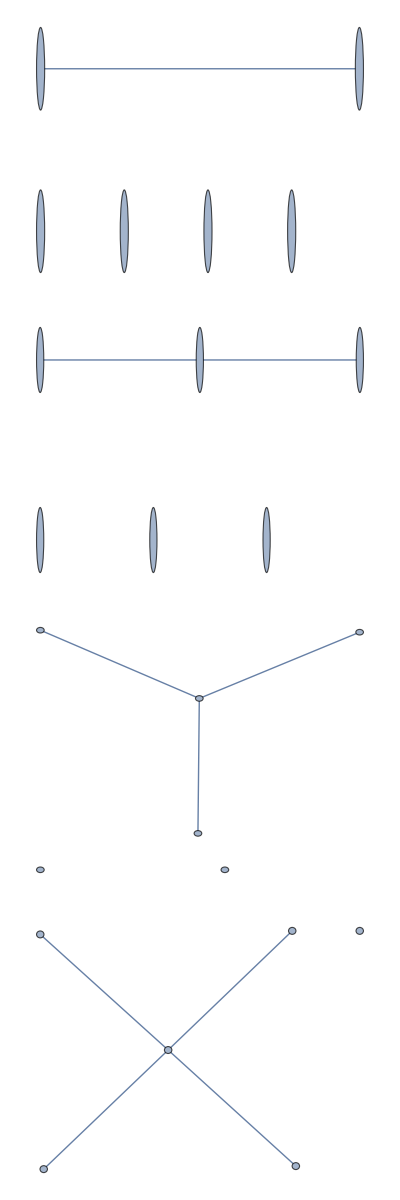

```mathematica
graph6[[;;5]]//Column
```

### 1.3 判别子图-从SE获取

#### 获取子图-从SE获取

```mathematica
ClearAll[FindSubgraph];
FindSubgraph[big_?UndirectedGraphQ,small_?UndirectedGraphQ]:=Module[{vl=VertexList[small],el=EdgeList[small],v,pv,e,pe},v=Table[Unique[],{Length@vl}];
pv=Pattern[#,_]&/@v;
e=Table[Unique[],{Length@el}];
Graph[Sort[Sort/@EdgeList[big]]/.Riffle[MapThread[Pattern,{e,Sort[Sort/@el]}]/.Thread[vl->pv],___,{1,-1,2}]->e]]
```

#### 测试函数

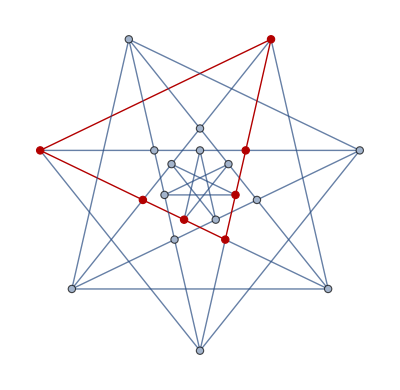

```mathematica
bmg=GraphData["BrinkmannGraph"];
HighlightGraph[bmg,FindSubgraph[bmg,Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->7,7<->1}]]]
```

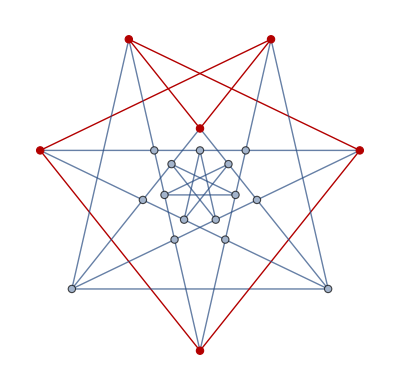

```mathematica
HighlightGraph[bmg,FindSubgraph[bmg,Graph[{"ape"<->"nut","nut"<->"mouse","mouse"<->"dad","dad"<->"sheep","sheep"<->"goat","goat"<->"ape"}]]]
```

#### 判断子图

```mathematica
SubgraphIsomorphismQ[big_?UndirectedGraphQ,small_?UndirectedGraphQ]:=Length[EdgeList@FindSubgraph[big,small]]==Length[EdgeList@small];
```

```mathematica
SubgraphIsomorphismQ[CompleteGraph[4],CompleteGraph[3]]
SubgraphIsomorphismQ[bmg,CompleteGraph[3]]
```

True

False

### 1.4 判别子图-从Github获取

#### 定义函数

```mathematica
Needs["IGraphM`"]
graph=CompleteGraph[5];
g2=CompleteGraph[4];
IGSubisomorphicQ[g2,graph]
```

True

## 2. 问题开始

### 2.1 导入函数

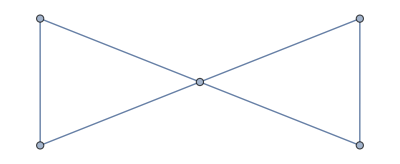

```mathematica
Needs["IGraphM`"];
gSet[n_]:=Import["http://cs.anu.edu.au/~bdm/data/graph"<>ToString@n<>".g6"]
(*Unprotect[IGSubisomorphicQ];
IGSubisomorphicQ[subgraph_][graph_]:=IGSubisomorphicQ[subgraph,graph];
Protect[IGSubisomorphicQ];*)
subgraph=Graph[{1<->2,2<->3,1<->3,4<->5,4<->3,5<->3}]
```

### 2.2 计算数据

#### n = 5

```mathematica
graphs=gSet[5];
```

7

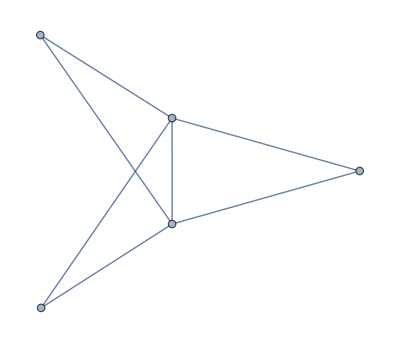
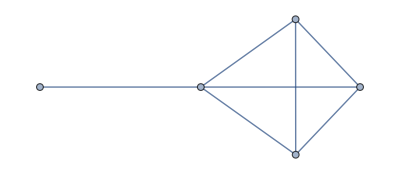
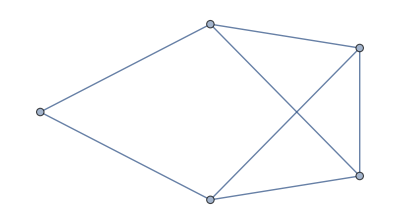

```mathematica
selected=Select[graphs,!IGSubisomorphicQ[subgraph,#]&];
m=(EdgeCount/@selected)//Max
Select[selected,EdgeCount@#==m&]
```